# QNM Amplitude: Time and Frequency domain analysis

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
<<MaTeX`
SetDirectory[NotebookDirectory[]];
$Assumptions={M>0}
DirName=NotebookDirectory[];
```

{M>0}

## Parameters

## Physical Parameters

### Wave equation Parameters

```mathematica
Mbh=rh/2;
λ=rh;
spin=2;
l=2;
```

### Bump Parameters

```mathematica
ModelName="BumpPT";
 ao= 10;(*115722/10000;*) (*120000/10000;*)
 ϵ= 0;(*204/100000;*)
```

## Numerical Parameters

```mathematica
Prec=10*MachinePrecision;


Nz$dom0=75;
Nz$dom1=75;


Nz$QNMload$dom0=75;
Nz$QNMload$dom1=75;
```

### QNM Selection

```mathematica
N$QNM$max=3;
```

## Schwarzschild Spacetime

## Metric Function

```mathematica
a=1-rh/r;
b=a;
f=FullSimplify[Sqrt[a*b], Assumptions->{rh>0, r>rh}];
ζ$of$r=FullSimplify[Sqrt[a/b], Assumptions->{rh>0, r>rh}];
```

```mathematica
m=r/2*(1-b);

fAsymp=Normal@Series[f,{r,Infinity,1}]//Expand;
M$ADM=-Coefficient[fAsymp,r,-1]/2//FullSimplify;
SubsM={M->M$ADM}
```

{M→rh/2}

## Hyperboloidal Formulation

## Radial Compactfication

### Areal Radius

```mathematica
ρ1=0;(*rh/λ 1/(1-σ0)*)
ρ0=rh/λ-ρ1;

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify;
```

### Radial Mapping

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ;
dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]];
```

```mathematica
σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]];
```

### Metric function and deviation function in compact coordinate

```mathematica
F=Simplify[f/.r->r$of$σ[σ]];
ζ=Simplify[ζ$of$r/.r->r$of$σ[σ]];
```

#### Find Horizons

```mathematica
SubsσHrz=Solve[{F==0, σ>0},σ,Reals];
σHrz=σ/.SubsσHrz;
nHrz=Length@σHrz;
rHrz=r$of$σ[σHrz];
```

#### Representation as in eq. 2.13 - Event Horizon

```mathematica
root$rh=(1-rHrz/r)/.r->r$of$σ[σ]//FullSimplify;
Kh=Expand[F/root$rh]//FullSimplify;
```

## Dimensionless Tortoise Coordinate

### Differential Equation (eq. 2.11)

```mathematica
dx$dσ=FullSimplify[-β/(σ^2F)];
```

### Contribution from Infinity (eq. 4.7)

```mathematica
x$0=ρ0/σ-2M/λ Log[σ];
dx0$dσ=FullSimplify[D[x$0,σ]];
```

### Contribution from Event Horizon (eq. 4.5)

```mathematica
KBHHrz=Table[Limit[Kh[[i]],SubsσHrz[[i]]],{i,1,nHrz}];
x$BHHrz=Table[rHrz[[i]]/(λ*KBHHrz[[i]])*Log[σHrz[[i]]-σ],{i,1,nHrz}];

dx$BHHrz$dσ=Table[D[x$BHHrz[[i]],σ],{i,1,nHrz}];
```

### Regular Contribution

```mathematica
dx$dσ$Reg=dx$dσ-dx0$dσ - Sum[dx$BHHrz$dσ[[i]],{i,1,nHrz}]/.SubsM;
Subs$dxdσ$Reg=x$Reg'[σ]->dx$dσ$Reg;
```

#### Check Tortoise

```mathematica
x$Reg[σ_]:=0;
x=x$0+ Sum[x$BHHrz[[i]],{i,1,nHrz}]+x$Reg[σ]/.SubsM//Simplify;
dx$dσ$Paper=D[x,σ]/.Subs$dxdσ$Reg;
FullSimplify[dx$dσ$Paper==dx$dσ]
```

True

## Height Function

### Out-In Strategy

```mathematica
H=-x$0 +Sum[x$BHHrz[[i]],{i,1,nHrz}]-x$Reg[σ]/.SubsM//Simplify;
dH$dσ=D[H,σ]/.Subs$dxdσ$Reg;
```

### Metric Functions

```mathematica
p=FullSimplify[-1/dx$dσ]
(*Plot[p/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

-((-1+σ) σ^2)

```mathematica
γ=dH$dσ*p//FullSimplify
(*Plot[γ/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

1-2 σ^2

```mathematica
(*Series[γ,{σ,σHrz[[1]],0}]*)
w=(1-γ^2)/p//FullSimplify
(*Plot[w/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->{0,All}]*)
```

4 (1+σ)

## Wave Equation

## Regge Wheeler Potential

```mathematica
If[spin==0,VRW=a/r^2*(l*(l+1) + r*D[a*b,r]/(2*a))];
If[Abs@spin==2, VRW=a/r^2* ( l*(l+1) - 6m/r + D[m,r])];

qRW=λ^2/p * VRW/.r->r$of$σ[σ]//FullSimplify
```

6-3 σ

### Bump

```mathematica
Vbump =  λ^(-2) Sech[x-ao]^2/.r->r$of$σ[σ]//FullSimplify;
(* λ^(-2) Exp[ -(x-ao)^2/(2 δ)  ]*)

qBump=λ^2/p * Vbump;
```

```mathematica
If[ϵ==0,
σBump=1/2,
σBump=σ/.N[Solve[x-ao==0,σ],50*MachinePrecision][[1]]
];
```

### Final Potential

```mathematica
V = VRW + ϵ Vbump/.r->r$of$σ[σ];
q = λ^2/p * V//FullSimplify;
```

## Functions in Wave Equation

```mathematica
W=w;

α2=p;
α1=D[p,σ];
α0=-q;

β1=2 γ;
β0=D[γ,σ];
```

## QNM Eigenfunctions

## Discrete Functions and Matrices

### AnMR

```mathematica
x$of$χ[χ_,κ_,xb_]:= xb(1- 2 Sinh[ κ (1-xb χ)]/Sinh[2κ]    );
χ$of$x[X_,κ_,xb_]:=xb*(1-ArcSinh[(1 - X*xb)*Sinh[2κ]/2]/κ);
```

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_, κ_, xb_, Prec_]:=Module[
{nc, Nc, χ, y},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);
χ=χ$of$x[y,κ,xb];

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,χ],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
x=.

zi=0;
zp=σBump;
zf=1;

Δz$dom0=zp-zi;
Δz$dom1=zf-zp;


nz$dom0=Nz$dom0+1; (*Total number of points*)
nz$dom1=Nz$dom1+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];

χ$dom0=N[Table[x[i,Nz$dom0],{i,0,Nz$dom0}],Prec];
χ$dom1=N[Table[x[i,Nz$dom1],{i,0,Nz$dom1}],Prec];

ZeroArray$dom0=ConstantArray[0,nz$dom0];
ZeroArray$dom1=ConstantArray[0,nz$dom1];
```

#### AnMR Parameter

DOMAIN 0 σ ∈ [0, σbump]

```mathematica
xb$dom0=1;

κ$dom0=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

If[κ$dom0==0,
X$dom0=χ$dom0;
XRef$dom0=χRef$dom0,

X$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χ$dom0)]/Sinh[2*κ$dom0]),Prec];
XRef$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χRef$dom0)]/Sinh[2*κ$dom0]),Prec];
];
z$dom0=N[zi+1/2 Δz$dom0*(1+X$dom0),Prec];
zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];
```

DOMAIN 1 σ ∈ [σbump,1]

```mathematica
xb$dom1=-1;
κ$dom1=125/100 * ao^(3/10);
If[κ$dom1==0,
X$dom1=χ$dom1
XRef$dom1=χRef$dom1
,
X$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χ$dom1)]/Sinh[2*κ$dom1]),Prec];
XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];
];
z$dom1=N[zp+1/2 Δz$dom1*(1+X$dom1),Prec];
zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];
```

### Differentiation Matrices

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

Domain 0

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom0=DiffMatrix[-1,1,Nz$dom0,Prec]; 
D2χ$dom0=Dχ$dom0 . Dχ$dom0;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom0],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom0=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom0=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom0=IdentityMatrix[nz$dom0];
Zero$dom0=ConstantArray[0,{nz$dom0,nz$dom0}];
Zero$dom0dom1=ConstantArray[0,{nz$dom0,nz$dom1}];
```

Loading Differentiation Matrices

Domain 1

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom1=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom1=Dχ$dom1 . Dχ$dom1;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom1],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom1=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom1=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom1=IdentityMatrix[nz$dom1];
Zero$dom1=ConstantArray[0,{nz$dom1,nz$dom1}];
Zero$dom1dom0=ConstantArray[0,{nz$dom1,nz$dom0}];
```

Loading Differentiation Matrices

#### Map derivatives δχ into δx

Domain 0

```mathematica
If[κ$dom0==0,
Dx$dom0=Dχ$dom0;
D2x$dom0=D2χ$dom0;

DxRef$dom0=DχRef$dom0;
D2xRef$dom0=D2χRef$dom0;

,

J =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2 =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

Dx$dom0 = N[Dχ$dom0/J,Prec];
D2x$dom0 = N[(D2χ$dom0 - J2*Dx$dom0)/J^2,Prec];

JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];
];
```

Domain 1

```mathematica
If[κ$dom1==0,
Dx$dom1=Dχ$dom1;
D2x$dom1=D2χ$dom1;

DxRef$dom1=DχRef$dom1;
D2xRef$dom1=D2χRef$dom1
,

J =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2 =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

Dx$dom1 = N[Dχ$dom1/J,Prec];
D2x$dom1 = N[(D2χ$dom1 - J2*Dx$dom1)/J^2,Prec];

JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];
];
```

#### Re-scale Derivative Operators

```mathematica
Dσ$dom0=2/Δz$dom0 * Dx$dom0;
D2σ$dom0=(2/Δz$dom0)^2 * D2x$dom0;

DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;
```

```mathematica
Dσ$dom1=2/Δz$dom1 * Dx$dom1;
D2σ$dom1=(2/Δz$dom1)^2 * D2x$dom1;

DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;
```

#### TEST OPERATORS

(SET TO NON-EVALUATED: CHANGE IF NEED TO TEST)

```mathematica
(*fTest[σ_]:=Cos[2*π*σ]*Exp[-σ^2]*)
(*fVec$dom0=fTest[z$dom0];*)
(*fVec$dom1=fTest[z$dom1];*)
(**)
(*Error$dσ$dom0=Total[Dσ$dom0 . fVec$dom0-fTest'[z$dom0]]*)
(*Error$dσ$dom1=Total[Dσ$dom1 . fVec$dom1-fTest'[z$dom1]]*)
(**)
(**)
(*Error$dσdσ$dom0=Total[Dσ$dom0 . Dσ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$dσdσ$dom1=Total[Dσ$dom1 . Dσ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
(**)
(**)
(*Error$d2σ$dom0=Total[D2σ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$d2σ$dom1=Total[D2σ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
```

### Discrete Functions

```mathematica
α2$dom0=α2/.σ->z$dom0;
α1$dom0=α1/.σ->z$dom0;
α0$dom0=Limit[α0, σ->z$dom0, Direction->"FromAbove"];

β1$dom0=β1/.σ->z$dom0;
β0$dom0=β0/.σ->z$dom0;
W$dom0=W/.σ->z$dom0;


α2$dom1=α2/.σ->z$dom1;
α1$dom1=α1/.σ->z$dom1;
α0$dom1=Limit[α0, σ->z$dom1, Direction->"FromBelow"];

β1$dom1=β1/.σ->z$dom1;
β0$dom1=β0/.σ->z$dom1;

W$dom1=W/.σ->z$dom1;
```

## QNM Eigenvalue Problem (Load Data)

### Discrete ODE operators ( - NOTE: TIME DOMAIN WAVE EQUATION IS NOT DIVIDED BY w(σ); - L matrix is not needed as we wil import QNM data )

```mathematica
L1$dom0=(α2$dom0*D2σ$dom0 + α1$dom0*Dσ$dom0 + α0$dom0*Id$dom0);
L2$dom0=( β1$dom0*Dσ$dom0 + β0$dom0*Id$dom0);

L1$dom1=(α2$dom1*D2σ$dom1 + α1$dom1*Dσ$dom1 + α0$dom1*Id$dom1);
L2$dom1=( β1$dom1*Dσ$dom1 + β0$dom1*Id$dom1);
```

### Load Eigenvalues and Eigenfunctions generated with BH_QNM_Eigenvalue.nb

```mathematica
n$QNM$max=N$QNM$max+1;
n$QNM=Range[0,N$QNM$max];

DirName$InputData="QNM_Eigenfunctions/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];
```

```mathematica
Nz=Nz$QNMload$dom0;
fn=Table[DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom0=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom0=Table[Delete[QNM$EigensytemData$dom0[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom0[[iQNM,1,2]]+I*QNM$EigensytemData$dom0[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom0=Table[QNM$EigensytemData$dom0[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom0[σ_, n_]:=ChebInterpolation[cREϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0, Prec]+I*ChebInterpolation[cIMϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0,Prec]
Plot$ϕQNM$Func$dom0=Table[Plot[Re@ϕQNM$Func$dom0[σ, n],{σ,zi,zp}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];

ϕQNM$dom0=Table[ϕQNM$Func$dom0[z$dom0,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom0=Conjugate[ϕQNM$dom0];
```

{QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n3_l2_spin2_Prec_159.546.dat}

QNM s

{-0.177925-0.747343 ⅈ,-0.54783-0.693422 ⅈ,-0.956554-0.602107 ⅈ,-1.41029+0.50301 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

```mathematica
Nz=Nz$QNMload$dom1;

fn=Table[DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom1=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom1=Table[Delete[QNM$EigensytemData$dom1[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom1[[iQNM,1,2]]+I*QNM$EigensytemData$dom1[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom1=Table[QNM$EigensytemData$dom1[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom1[σ_, n_]:=ChebInterpolation[cREϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]+I*ChebInterpolation[cIMϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]
Plot$ϕQNM$Func$dom1=Table[Plot[Re@ϕQNM$Func$dom1[σ, n],{σ,zp,zf}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];


ϕQNM$dom1=Table[ϕQNM$Func$dom1[z$dom1,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom1=Conjugate[ϕQNM$dom1];
```

{QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n3_l2_spin2_Prec_159.546.dat}

QNM s

{-0.177925-0.747343 ⅈ,-0.54783-0.693422 ⅈ,-0.956554-0.602107 ⅈ,-1.41029+0.50301 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

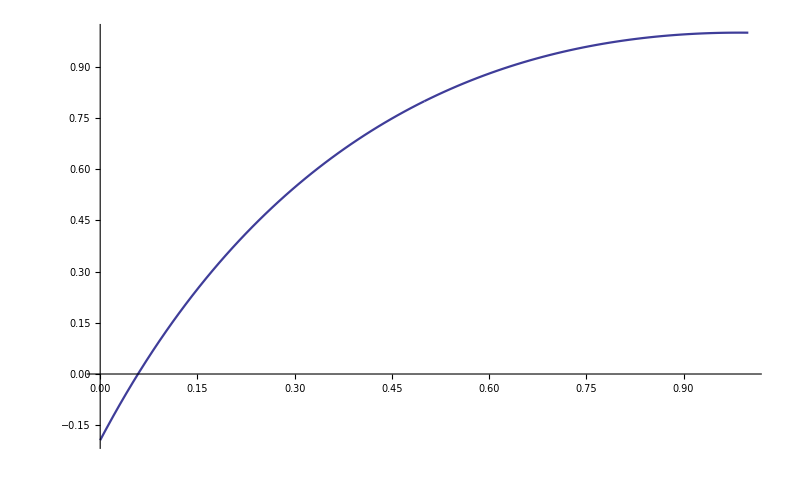

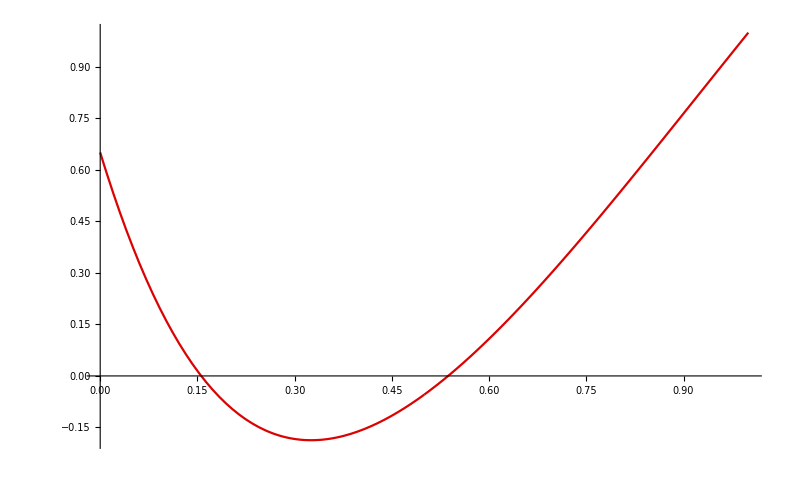

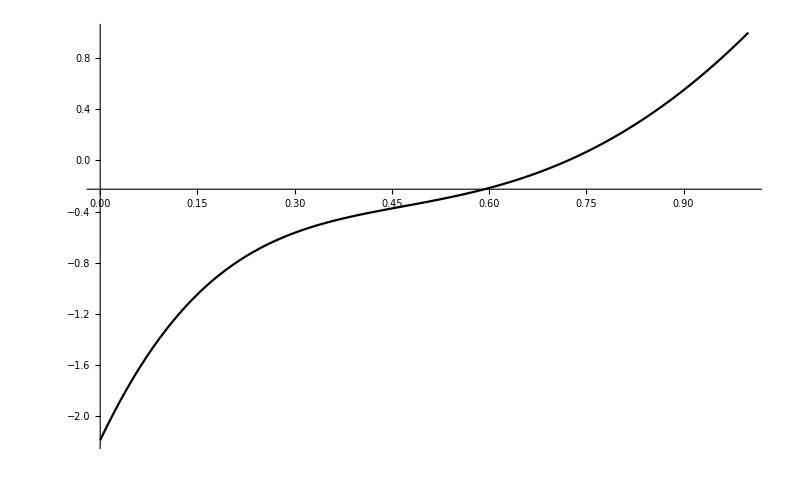

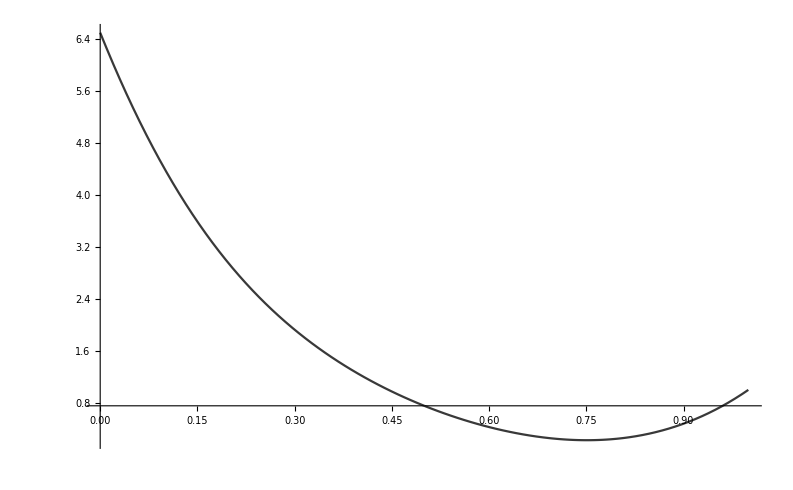

Part::partw: Part 5 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

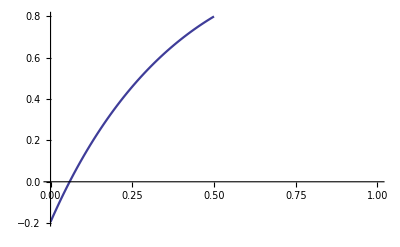
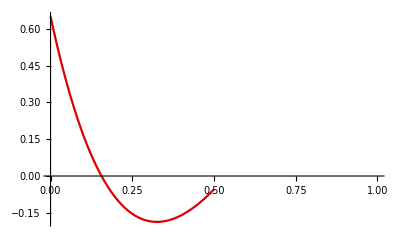
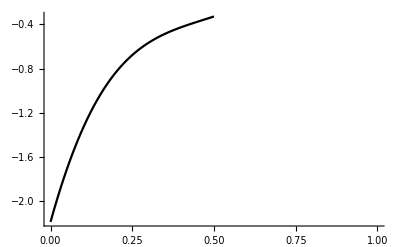
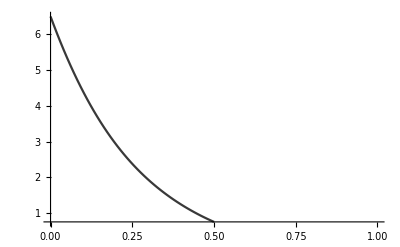
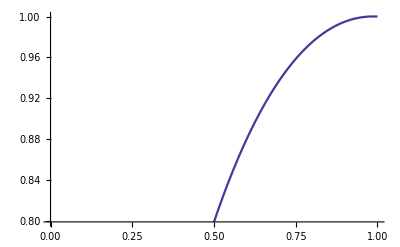
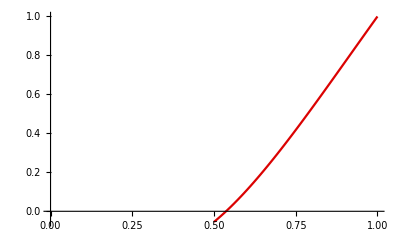
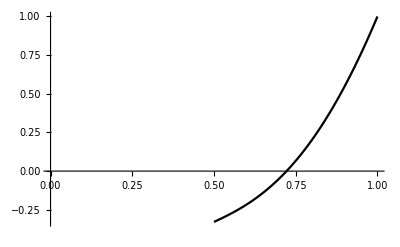
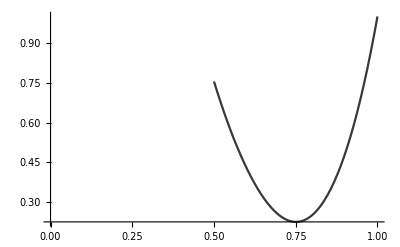
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦5⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦5⟧]

Part::partw: Part 6 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦6⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦6⟧]

Part::partw: Part 7 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦7⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦7⟧]

Part::partw: Part 8 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦8⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦8⟧]

Part::partw: Part 9 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦9⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦9⟧]

```mathematica
Show[Plot$ϕQNM$Func$dom0[[1]],Plot$ϕQNM$Func$dom1[[1]]]
Show[Plot$ϕQNM$Func$dom0[[2]],Plot$ϕQNM$Func$dom1[[2]]]
Show[Plot$ϕQNM$Func$dom0[[3]],Plot$ϕQNM$Func$dom1[[3]]]
Show[Plot$ϕQNM$Func$dom0[[4]],Plot$ϕQNM$Func$dom1[[4]]]
Show[Plot$ϕQNM$Func$dom0[[5]],Plot$ϕQNM$Func$dom1[[5]]]
Show[Plot$ϕQNM$Func$dom0[[6]],Plot$ϕQNM$Func$dom1[[6]]]
Show[Plot$ϕQNM$Func$dom0[[7]],Plot$ϕQNM$Func$dom1[[7]]]
Show[Plot$ϕQNM$Func$dom0[[8]],Plot$ϕQNM$Func$dom1[[8]]]
Show[Plot$ϕQNM$Func$dom0[[9]],Plot$ϕQNM$Func$dom1[[9]]]
```

## QNM Amplitudes

## QNM Excitation Operators

### Operators

```mathematica
A$dom0[s_]:=- W$dom0*s^2*Id$dom0 + L1$dom0 + s*L2$dom0;
c$dom0[s_, sQNM_]:=L2$dom0- W$dom0*(s+sQNM)*Id$dom0;
B$dom0[s_,V0_,W0_]:=L2$dom0 . V0 - W$dom0*(s*V0 + W0);

A$dom1[s_]:=- W$dom1*s^2*Id$dom1 + L1$dom1 + s*L2$dom1;
c$dom1[s_, sQNM_]:=L2$dom1- W$dom1*(s+sQNM)*Id$dom1;
B$dom1[s_,V0_,W0_]:=L2$dom1 . V0 - W$dom1*(s*V0 + W0);
```

#### Choose QNM

```mathematica
An$dom0=Table[A$dom0[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom0=Table[c$dom0[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom0[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom1=Table[A$dom1[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom1=Table[c$dom1[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom1[[iQNM]],{iQNM,1,n$QNM$max}];

(*An$Conj=Table[A[s$QNM$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$Conj=Table[c[s$QNM$Conj[[iQNM]],s$QNM$Conj[[iQNM]]].ϕQNM$Conj$Vec[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

#### Multidomain Matrix

```mathematica
An=Table[ N[ArrayFlatten[{
{   An$dom0[[iQNM]]    ,       Zero$dom0dom1   } , 
{  Zero$dom1dom0,   An$dom1[[iQNM]] } 
}],
Prec],
{iQNM,1,n$QNM$max}
];




Cn=Table[ Join[Cn$dom0[[iQNM]],Cn$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];
```

#### Continuity of Auxiliary function at Boundary Domain

```mathematica
An[[All,1,All]]=0;
An[[All,1,1]]=1;
An[[All,1,-1]]=-1;

Cn[[All,1]]=0;
```

#### Continuity of Auxiliary function’s derivative at Boundary Domain

```mathematica
An[[All,nz$dom0 + nz$dom1,All]]=0;
An[[All,nz$dom0 + nz$dom1, ;;nz$dom0]]=Dσ$dom0[[1, All]];
An[[All,nz$dom0 + nz$dom1, nz$dom0+1;;nz$dom0+nz$dom1 ]]=-Dσ$dom1[[-1, All]];

Cn[[All,-1]]=0;
```

### Amplitude Matrix

```mathematica
m1t =Table[Join[Transpose@An[[iQNM]], {Cn[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1 =Table[Transpose[m1t[[iQNM]]],{iQNM,1,n$QNM$max}];

δ=Table[KroneckerDelta[i,nz$dom0+1],{i,1,nz$dom0+nz$dom1+1}];

Mamp=Table[Join[m1[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
MampInv=ParallelTable[Inverse@Mamp[[iQNM]],{iQNM,1,n$QNM$max}];


(*m1t$Conj=Table[Join[Transpose@An$Conj[[iQNM]], {Cn$Conj[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1$Conj =Table[Transpose[m1t$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];

Mamp$Conj=Table[Join[m1$Conj[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
Mamp$ConjInv=ParallelTable[Inverse@Mamp$Conj[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

## Calculate QNM Amplitude

### Initial Data

```mathematica
ϕ0$dom0=ϕQNM$dom0;(*ConstantArray[1,nz$dom0];*) (*2*Re[ϕQNM$dom0];*) 
ψ0$dom0=ϕQNM$dom0*s$QNM; (*ConstantArray[0,nz$dom0];*)(*2*Re[ϕQNM$dom0*s$QNM];*) 

ϕ0$dom1=ϕQNM$dom1; (*ConstantArray[1,nz$dom1];*) (*2*Re[ϕQNM$dom1];*) 
ψ0$dom1= ϕQNM$dom1*s$QNM;(*2*Re[ϕQNM$dom1*s$QNM];*)
```

#### Source Function ID

```mathematica
Bn$dom0=Table[B$dom0[s$QNM[[iQNM]],ϕ0$dom0[[iQNM]],ψ0$dom0[[iQNM]]],{iQNM,1,n$QNM$max}];
Bn$dom1=Table[B$dom1[s$QNM[[iQNM]],ϕ0$dom1[[iQNM]],ψ0$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];

Bn=Table[Join[Bn$dom0[[iQNM]],Bn$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];
(*Bn$Conj=Table[B[s$QNM$Conj[[iQNM]],ϕ0,ψ0],{iQNM,1,n$QNM$max}];*)

Bn[[All,1]]=0;
Bn[[All,-1]]=0;
```

### Total Source

```mathematica
g0=1;

S=Table[Append[Bn[[iQNM]] , g0],{iQNM,1,n$QNM$max}];
(*S$Conj=Table[Append[Bn$Conj[[iQNM]] +S2ndOrder$Vec[s$QNM$Conj[[iQNM]]], g0],{iQNM,1,n$QNM$max}];*)
```

#### Amplitude

```mathematica
ηSol=Table[MampInv[[iQNM]].S[[iQNM]],{iQNM,1,n$QNM$max}];

η=ηSol[[All,nz$dom0+nz$dom1+1]];


ϕScri=ϕQNM$dom0[[All,nz$dom0]];
ϕHrz=ϕQNM$dom1[[All,1]];

ηϕScri=Table[ η[[iQNM]] * ϕScri[[iQNM]],{iQNM,1,n$QNM$max}];
ηϕHrz =Table[ η[[iQNM]] * ϕHrz[[iQNM]],{iQNM,1,n$QNM$max}];

ηϕScri;
Abs[ηϕHrz];
N[η]
```

{1.+5.13985×10^-41 ⅈ,1.-7.26488×10^-37 ⅈ,1.+1.02921×10^-33 ⅈ,1.+8.20572×10^-31 ⅈ}

{-2.22306×10^-40+5.13985×10^-41 ⅈ,2.9996×10^-37-7.26488×10^-37 ⅈ,1.76884×10^-34+1.02921×10^-33 ⅈ,-2.14434×10^-31+8.20572×10^-31 ⅈ}

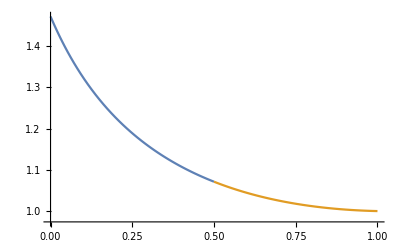

```mathematica
ψ$s=ηSol[[All,1;;nz$dom0+nz$dom1]];
ψ$s$dom0=ηSol[[All,1;;nz$dom0]];
ψ$s$dom0$Data=Table[Transpose@{z$dom0,Abs@ψ$s$dom0[[iQNM]]},{iQNM,1,n$QNM$max}];
ψ$s$dom1=ηSol[[All,nz$dom0+1;;nz$dom0+nz$dom1]];
ψ$s$dom1$Data=Table[Transpose@{z$dom1,Abs@ψ$s$dom1[[iQNM]]},{iQNM,1,n$QNM$max}];
ListPlot[{ψ$s$dom0$Data[[1]],ψ$s$dom1$Data[[1]]}, Joined->True]
```

```mathematica
z$dom0[[-1]]
```

0.

```mathematica
ϕQNM$dom0[[1,-1]]
ϕQNM$dom1[[1,1]]
```

-0.1939387559047354941132364848184810595255462955500882999273681248125034254582655468039545096418981085169539223482557838902466691557809978448557492784-1.4585543303754840361500113251619001410951858862026731236037148268561708059326724473845563098964349230031261865619707063814127358529893413703638586933 ⅈ

1.+0. ⅈ

```mathematica
ψ$s[[1,-1]]
```

0.79916214035294916701034606122907715995082911784697021269188118664270682760190729422881051102224442190942684802809127417992859328014138868647699-0.71321916340705787104282307223546388343297240157802586301003758309400313615524505311869142574294928055519828331967025014522023312937018519880158 ⅈ